```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

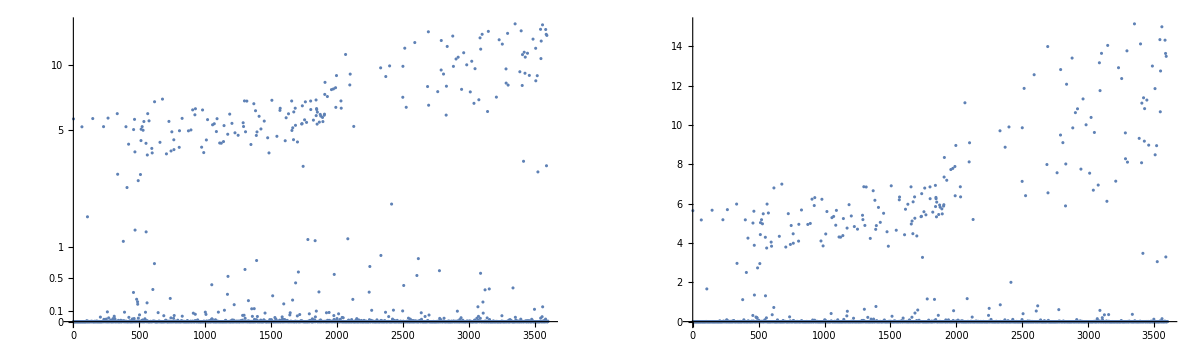

```mathematica
GraphicsGrid[{{
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -21.569243903
L2PhaseSet : -38.2287099343
S1ELkG : 1787.5873712192
S2ELkG : -3142.3836347712
S3ELkG : -1074.0050500477
S1EL_xOffset : 0.0009468429
S1EL_yOffset : 0.0000324051
S2EL_xOffset : -0.0003516496
S2EL_yOffset : 0.0001947908
S2ER_xOffset : -0.0001541918
S2ER_yOffset : -0.0013554862
S1ER_xOffset : 0.0012609467
S1ER_yOffset : -0.000939387
PDrive_median_x : 8.56e-8
PDrive_median_y : -2.6534e-6
PDrive_median_xp : -0.0000437986
PDrive_median_yp : -2.0303e-6
PDrive_sigmaSI90_x : 0.0000221995
PDrive_sigmaSI90_y : 0.0000175726
PDrive_sigmaSI90_z : 0.0000176295
PDrive_sigmaSI90_xp : 0.0000897245
PDrive_sigmaSI90_yp : 0.0000244498
PDrive_emitSI90_x : 0.0000386136
PDrive_emitSI90_y : 4.998e-6
PDrive_norm_emit_x : 0.0000433781
PDrive_norm_emit_y : 6.6349e-6
PDrive_zCentroid : 991.33129979
PDrive_charge_nC : 1.19687568
PDrive_BMAG_x : 1.1383271402
PDrive_BMAG_y : 2.1320182056
PDrive_sliced_BMAG_x : List(2.9495761149,3.6746488598,2.780567697,1.9310897785,2.0650331759)
PDrive_sliced_BMAG_y : List(1.097104812,3.1311791489,5.8263068053,6.1097298191,3.0377373831)
PWitness_median_x : -3.5496e-6
PWitness_median_y : 6.195e-7
PWitness_median_xp : 0.0000936333
PWitness_median_yp : -0.0000111186
PWitness_sigmaSI90_x : 0.0000139205
PWitness_sigmaSI90_y : 0.0000160498
PWitness_sigmaSI90_z : 0.000010872
PWitness_sigmaSI90_xp : 0.0000516233
PWitness_sigmaSI90_yp : 0.000058389
PWitness_emitSI90_x : 6.6883e-6
PWitness_emitSI90_y : 2.2193e-6
PWitness_norm_emit_x : 8.6176e-6
PWitness_norm_emit_y : 9.9694e-6
PWitness_zCentroid : 991.3314283733
PWitness_charge_nC : 0.40391568
PWitness_BMAG_x : 2.459082282
PWitness_BMAG_y : 3.5491301953
PWitness_sliced_BMAG_x : List(2.0048352083,4.6566111724,2.6758625029,2.7136802254,2.3393833069)
PWitness_sliced_BMAG_y : List(2.7560757333,4.2057967794,3.5265017846,4.1150257371,3.572078681)
bunchSpacing : 0.0001285833
transverseCentroidOffset : 4.8914e-6
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.5285218178
errorTerm_secondaryObjective : 2.8346e-6
maximizeMe : 15.1364746445
inputBeamFilePathSuffix : "/beams/2024-10-14_Impact_TwoBunch/2024-10-14_TwoBunch.h5"
csrTF : False

## Plot specific

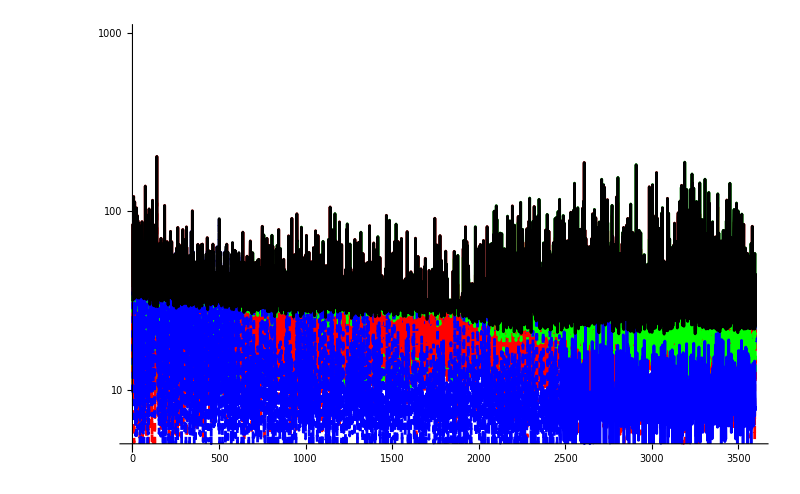

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{5,1000}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

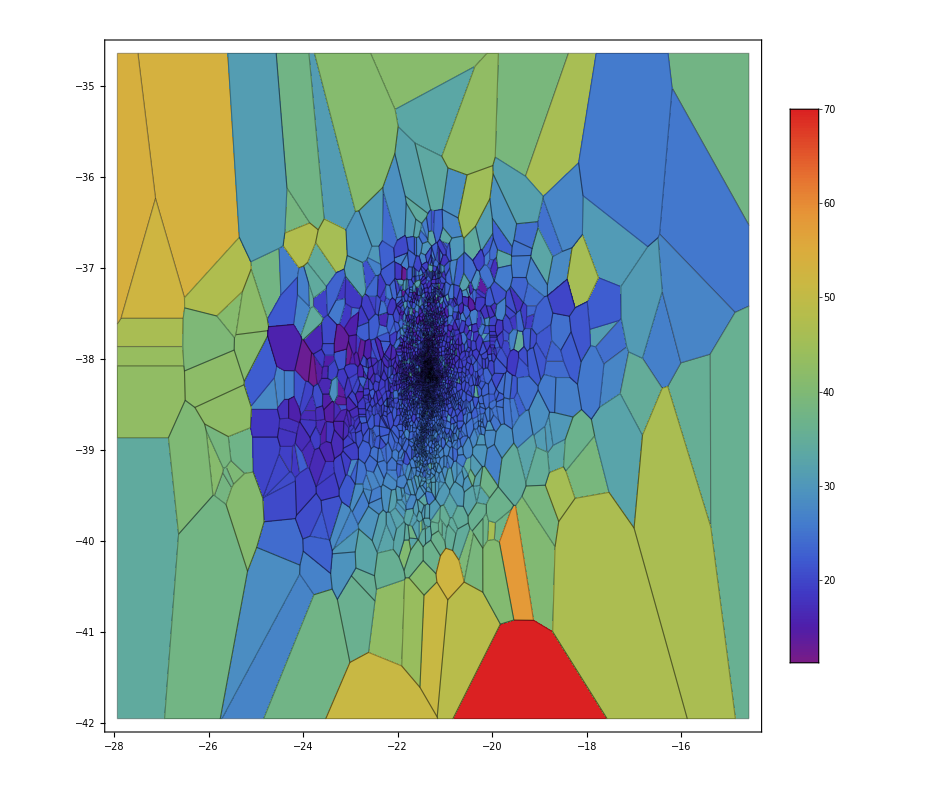

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->All,Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

## Plot all

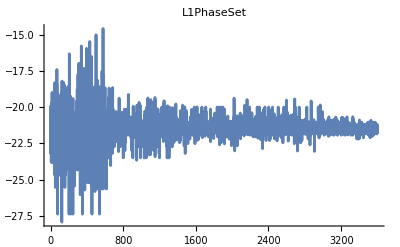
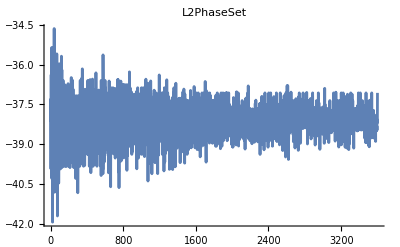
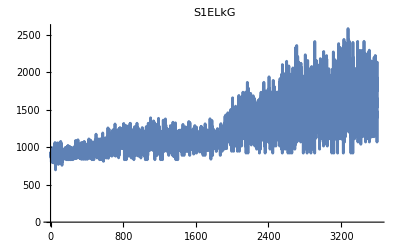
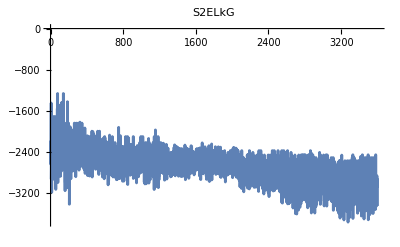
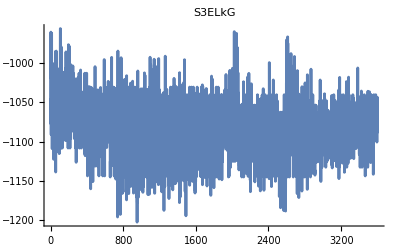
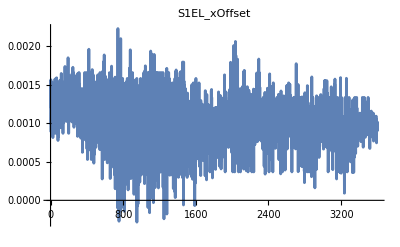
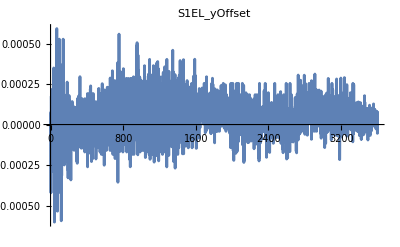
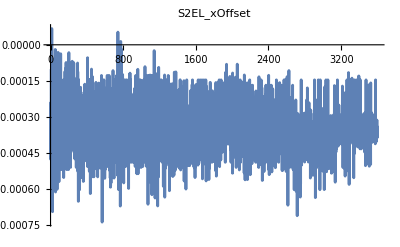
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -21.5692 | -1.2572
L2PhaseSet | -38.6737 | -38.2287 | 0.444996
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.000946843 | 0.000561588
S1EL_yOffset | -0.000241114 | 0.0000324051 | 0.000273519
S2EL_xOffset | -0.00141787 | -0.00035165 | 0.00106622
S2EL_yOffset | 0.0000111705 | 0.000194791 | 0.00018362
S2ER_xOffset | -0.00223816 | -0.000154192 | 0.00208397
S2ER_yOffset | -0.000675996 | -0.00135549 | -0.00067949
S1ER_xOffset | 0.00100714 | 0.00126095 | 0.00025381
S1ER_yOffset | 0.000398456 | -0.000939387 | -0.00133784
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]